```mathematica
Print["Running doApndxLiqConstr"];
(* This cell contains generic setup stuff to prepare for execution of the programs *)
ClearAll["Global`*"]; ParamsAreSet = False;
If[$VersionNumber < 6,(*then*) Print["These programs require Mathematica version 6 or greater."]; Abort[]];
(* If running from Notebook front end, set directory to Notebook's directory *)
If[Length[$FrontEnd] > 0, NBDir = SetDirectory[NotebookDirectory[]]];
(* If not running from Notebook front end, set directory manually *)
If[Length[$FrontEnd] == 0,SetDirectory["/Volumes/Data/Work/BufferStock/BufferStockTheory/Latest/Code/Mathematica/Results/BufferStockTheory"]];
SaveFigs = True;

HomeDir = Directory[];
CodeDir = HomeDir<>"/../../CoreCode";
CDToHomeDir := SetDirectory[HomeDir];
CDToCodeDir := SetDirectory[HomeDir<>"/../../CoreCode"];
CDToCodeDir;
<< SetupModelSolutionRoutines.m;
<< SetParamsToBaselineVals.m;
CDToHomeDir;
```

Running doApndxLiqConstr

Part::pkspec1: The expression LastPeriod cannot be used as a part specification.

{R,β,Γ,ρ}={1.02,0.980392,0.98,2}

PF-GIC fails (Γ < Þ):True

{Γ , Þ=(R)^(1/ρ) β^(1/ρ) , (R)}={0.98,1.,1.02}

Γ <((R) β)^(1/ρ)< R:True

RIC holds (Þ < R):True

⇒ FHWC holds (Γ < R):True

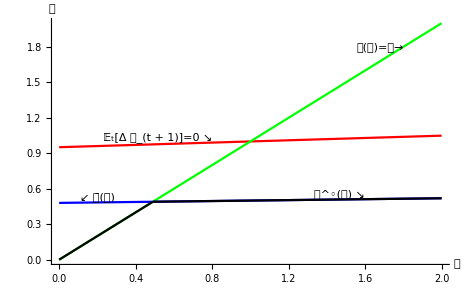

```mathematica
(* Example where PF-GIC fails but RIC holds *)
Clear[R,β,Γ,ρ,m♯,𝒸◦];
Print["{R,β,Γ,ρ}=",{R=1.02,β=1/1.02,Γ=0.98,ρ=2}];
Print["PF-GIC fails (Γ < Þ):" ,Γ < Þ];
Print["{Γ , Þ=(R)^(1/ρ) β^(1/ρ) , (R)}=",{Γ , (R)^(1/ρ) β^(1/ρ) , (R)}];
Print["Γ <((R) β)^(1/ρ)< R:",Γ <((R) β)^(1/ρ)< R];
Print["RIC holds (Þ < R):",  Þ <(R)];
Print[" ⇒ FHWC holds (Γ < R):",Γ < R];
m♯ = (ℏInf-1)(κMinInf/(1-κMinInf));
𝒸◦[𝓂_] := Min[𝓂,m♯ + κMinInf (𝓂-m♯)];
{mMinPlot,mMaxPlot}={0,2};
{cMinPlot,cMaxPlot}={mMinPlot,mMaxPlot};
PFGICFailsRICHoldsPlot = Plot[{𝒸SuchThat𝔼mtp1Equalsmt[m],m,𝒸ϝInf[m],𝒸◦[m]},{m,mMinPlot,mMaxPlot},PlotRange->All
,PlotStyle->{Red,Green,Blue,Black}
,AxesLabel->{"𝓂","𝒸"}];
Print[PFGICFailsRICHolds=Show[PFGICFailsRICHoldsPlot
,Graphics[Text["↙ 𝒸̄(𝓂)",{0.1mMaxPlot,𝒸ϝInf[0.1 mMaxPlot]},{0,-1}]]
,Graphics[Text["𝒸(𝓂)=𝓂→",{0.9mMaxPlot,0.9 mMaxPlot},{1,0}]]
,Graphics[Text["𝔼_t[Δ 𝓂_(t + 1)]=0 ↘",{0.4mMaxPlot,𝒸SuchThat𝔼mtp1Equalsmt[0.4 mMaxPlot]},{1,-1}]]
,Graphics[Text["𝒸^◦(𝓂) ↘",{0.8 mMaxPlot,𝒸◦[0.8 mMaxPlot]},{1,-1}]]
]
];
```

{R,β,Γ,ρ}={1.04,0.980392,1.02,2}

{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}={1.00976,1.02,1.04}

Þ < Γ < R:True

PF-GIC Holds (Þ < Γ):True

RIC holds (Þ < R):True

FHWC holds (Γ < R):True

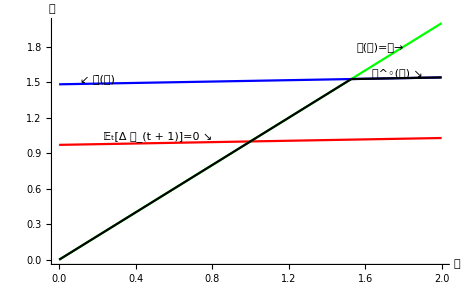

```mathematica
(* Example where PF-GIC, RIC, and FHWC all hold *)
Clear[R,β,Γ,ρ,m♯,𝒸◦];
Print["{R,β,Γ,ρ}=",{R=1.04,β=1/1.02,Γ=1.02,ρ=2}];
Print["{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}=",{(R)^(1/ρ) β^(1/ρ) , Γ , (R)}];
Print["Þ < Γ < R:",((R) β)^(1/ρ)< Γ < R];
Print["PF-GIC Holds (Þ < Γ):" , Þ< Γ];
Print["RIC holds (Þ < R):",  Þ <(R)];
Print["FHWC holds (Γ < R):",Γ < R];
m♯ = (ℏInf-1)(κMinInf/(1-κMinInf));
𝒸◦[𝓂_] := Min[𝓂,m♯ + κMinInf (𝓂-m♯)];
{mMinPlot,mMaxPlot}={0,2};
{cMinPlot,cMaxPlot}={mMinPlot,mMaxPlot};
PFGICHoldsRICHoldsPlot = Plot[{𝒸SuchThat𝔼mtp1Equalsmt[m],m,𝒸ϝInf[m],𝒸◦[m]},{m,mMinPlot,mMaxPlot},PlotRange->All
,PlotStyle->{Red,Green,Blue,Black}
,AxesLabel->{"𝓂","𝒸"}];
Print[PFGICHoldsRICHolds=Show[PFGICHoldsRICHoldsPlot
,Graphics[Text["↙ 𝒸̄(𝓂)",{0.1mMaxPlot,𝒸ϝInf[0.1 mMaxPlot]},{0,-1}]]
,Graphics[Text["𝒸(𝓂)=𝓂→",{0.9mMaxPlot,0.9 mMaxPlot},{1,0}]]
,Graphics[Text["𝔼_t[Δ 𝓂_(t + 1)]=0 ↘",{0.4mMaxPlot,𝒸SuchThat𝔼mtp1Equalsmt[0.4 mMaxPlot]},{1,-1}]]
,Graphics[Text["𝒸^◦(𝓂) ↘",{0.95mMaxPlot,𝒸◦[0.95 mMaxPlot]},{1,-1}]]
]
];
```

{R,β,Γ,ρ}={1.01,0.97,1.02,2}

Þ=(R)^(1/ρ) β^(1/ρ)=0.989798

PF-GIC holds (Þ < Γ):True

RIC holds (Þ < R):True

FHWC fails (R < Γ):True

PF-FVAC holds Þ/Γ < (R/Γ)^(1/ρ):True

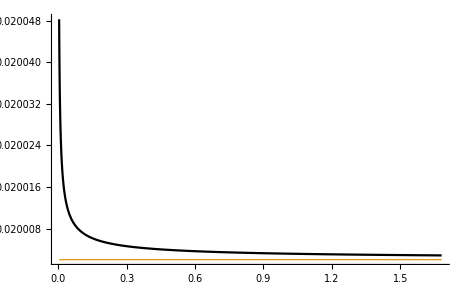

```mathematica
(* Example where PF-GIC holds, FHWC fails, RIC holds, PF-FVAC holds *)
(* Show MPC asymptotes to κMinInf *)
Clear[R,β,Γ,ρ,𝒸From𝒷,𝓃Approx,𝓃Exact];
𝓃Approx[𝒷_] :=If[𝒷+(1/(1-ℛ^-1))<=0,1,(Log[(-ÞRtn/(1-ÞRtn))+(-ℛ^-1/(1-ℛ^-1))]- Log[𝒷+(1/(1-ℛ^-1))])/Log[ℛ]];
𝓃Exact[𝒷_] :=nSeek /. FindRoot[b♯[nSeek] ==𝒷,{nSeek,Max[1,𝓃Approx[𝒷]]}];
𝒸From𝒷[𝒷_] := ÞΓPF^(-𝓃Exact[𝒷]);
Print["{R,β,Γ,ρ}=",{R= 1.01,β = 0.97,Γ=1.02,ρ=2}];
Print["Þ=(R)^(1/ρ) β^(1/ρ)=",(R)^(1/ρ) β^(1/ρ)];
Print["PF-GIC holds (Þ < Γ):" , Þ< Γ];
Print["RIC holds (Þ < R):",  Þ <(R)];
Print["FHWC fails (R < Γ):", R< Γ];
Print["PF-FVAC holds Þ/Γ < (R/Γ)^(1/ρ):",Þ/Γ<(R/Γ)^(1/ρ)];

{nMin,nMax}={300,500};
KinkPoints=Table[{b♯[n],c♯[n]},{n,nMin,nMax}];
KinkPointsFunc=Interpolation[KinkPoints,InterpolationOrder->2];
KinkPointsPlot=ListPlot[KinkPoints,PlotRange->All];
ComparePlots=Show[KinkPointsPlot,Plot[𝒸From𝒷[𝒷],{𝒷,b♯[nMin],b♯[nMax]}]];
Print[Plot[{KinkPointsFunc'[𝒷],κMinInf},{𝒷,b♯[nMin],b♯[nMax]},PlotRange->All]];
```

Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC Fails

{R,β,Γ,ρ}={0.98,0.99,1.,2}

{R,β,Γ,ρ}={0.98,1.,0.99,2}

{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}={0.989949,0.99,0.98}

PF-GIC holds (Þ < Γ):True

RIC fails (R < Þ):True

FHWC fails (R < Γ):True

PF-FVAC fails (R/Γ)^(1/ρ) < Þ/Γ (same as 1 < β Γ^(1 - ρ)):True

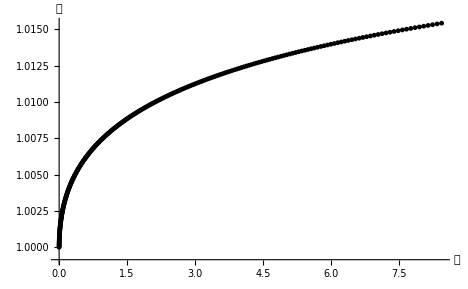

Exporting:./Figures/PFGICHoldsFHWCFailsRICFails

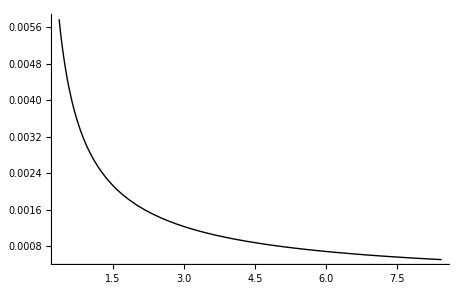

```mathematica
Print["Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC Fails"];
Clear[R,β,Γ,ρ,𝒸From𝒷,𝓃Approx,𝓃Exact];
𝓃Approx[𝒷_] :=If[𝒷+(1/(1-ℛ^-1))<=0,1,(Log[(-ÞRtn/(1-ÞRtn))+(-ℛ^-1/(1-ℛ^-1))]- Log[𝒷+(1/(1-ℛ^-1))])/Log[ℛ]];
𝓃Exact[𝒷_] :=nSeek /. FindRoot[b♯[nSeek] ==𝒷,{nSeek,Max[1,𝓃Approx[𝒷]]}];
𝒸From𝒷[𝒷_] := ÞΓPF^(-𝓃Exact[𝒷]);
Print["{R,β,Γ,ρ}=",{R=0.98,β = 0.99,Γ=1.0,ρ=2}];
Print["{R,β,Γ,ρ}=",{R,β,Γ,ρ}={0.98,1.00,0.99,2}];
Print["{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}=",{(R)^(1/ρ) β^(1/ρ) , Γ , (R)}];
Print["PF-GIC holds (Þ < Γ):" , Þ< Γ];
Print["RIC fails (R < Þ):",  (R) <Þ];
Print["FHWC fails (R < Γ):", R< Γ];
Print["PF-FVAC fails (R/Γ)^(1/ρ) < Þ/Γ (same as 1 < β Γ^(1 - ρ)):",1 <β Γ^(1-ρ)];
{nMin,nMax}={0,300};
KinkPoints=Table[{b♯[n],c♯[n]},{n,nMin,nMax}];
KinkPointsFunc=Interpolation[KinkPoints,InterpolationOrder->2];
KinkPointsPlot=ListPlot[KinkPoints,PlotRange->All];
cfbPlot=Plot[{𝒸From𝒷[𝒷]},{𝒷,b♯[nMin],b♯[nMax]}];
PFGICHoldsFHWCFailsRICFails=Show[KinkPointsPlot,cfbPlot
,AxesLabel->{"𝒷","𝒸"}
];
CDToHomeDir;
ExportFigs["PFGICHoldsFHWCFailsRICFails"];
Print[Plot[{KinkPointsFunc'[𝒷]},{𝒷,b♯[nMax-200],b♯[nMax]},PlotRange->All]];
```

Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC holds

{R,β,Γ,ρ}={0.98,0.99,1.,2}

{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}={0.984987,1.,0.98}

PF-GIC holds (Þ < Γ):True

RIC fails (R < Þ):True

FHWC fails (R < Γ):True

PF-FVAC holds  Þ/Γ < (R/Γ)^(1/ρ)):True

PFGICHoldsFHWCFailsRICPFVACHoldsFails

Exporting:./Figures/PFGICHoldsFHWCFailsRICPFVACHoldsFails

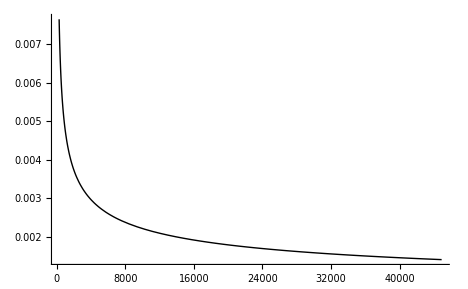

```mathematica
Print["Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC holds"];
Clear[R,β,Γ,ρ,𝒸From𝒷,𝓃Approx,𝓃Exact];
𝓃Approx[𝒷_] :=If[𝒷+(1/(1-ℛ^-1))<=0,1,(Log[(-ÞRtn/(1-ÞRtn))+(-ℛ^-1/(1-ℛ^-1))]- Log[𝒷+(1/(1-ℛ^-1))])/Log[ℛ]];
𝓃Exact[𝒷_] :=nSeek /. FindRoot[b♯[nSeek] ==𝒷,{nSeek,Max[1,𝓃Approx[𝒷]]}];
𝒸From𝒷[𝒷_] := ÞΓPF^(-𝓃Exact[𝒷]);
Print["{R,β,Γ,ρ}=",{R=0.98,β = 0.99,Γ=1.0,ρ=2}];
Print["{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}=",{(R)^(1/ρ) β^(1/ρ) , Γ , (R)}];
Print["PF-GIC holds (Þ < Γ):" , Þ< Γ];
Print["RIC fails (R < Þ):",  (R) <Þ];
Print["FHWC fails (R < Γ):", R< Γ];
Print["PF-FVAC holds  Þ/Γ < (R/Γ)^(1/ρ)):",β Γ^(1-ρ)<1];
{nMin,nMax}={0,300};
KinkPoints=Table[{b♯[n],c♯[n]},{n,nMin,nMax}];
KinkPointsFunc=Interpolation[KinkPoints,InterpolationOrder->2];
KinkPointsPlot=ListPlot[KinkPoints,PlotRange->All];
cfbPlot=Plot[{𝒸From𝒷[𝒷]},{𝒷,b♯[nMin],b♯[nMax]}];
PFGICHoldsFHWCFailsRICFailsPFVACHolds=Show[KinkPointsPlot,cfbPlot
,AxesLabel->{"𝓂","𝒸"}
];
CDToHomeDir;
ExportFigs["PFGICHoldsFHWCFailsRICPFVACHoldsFails"];
Print[Plot[{KinkPointsFunc'[𝒷]},{𝒷,b♯[nMax-200],b♯[nMax]},PlotRange->All]];
```

```mathematica
Print["Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC Fails"];
Clear[R,β,Γ,ρ,𝒸From𝒷,𝓃Approx,𝓃Exact];
𝓃Approx[𝒷_] :=If[𝒷+(1/(1-ℛ^-1))<=0,1,(Log[(-ÞRtn/(1-ÞRtn))+(-ℛ^-1/(1-ℛ^-1))]- Log[𝒷+(1/(1-ℛ^-1))])/Log[ℛ]];
𝓃Exact[𝒷_] :=nSeek /. FindRoot[b♯[nSeek] ==𝒷,{nSeek,Max[1,𝓃Approx[𝒷]]}];
𝒸From𝒷[𝒷_] := ÞΓPF^(-𝓃Exact[𝒷]);
Print["{R,β,Γ,ρ}=",{R,β,Γ,ρ}={0.98,1.00,0.99,2}];
Print["{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}=",{(R)^(1/ρ) β^(1/ρ) , Γ , (R)}];
Print["PF-GIC holds (Þ < Γ):" , Þ< Γ];
Print["RIC fails (R < Þ):",  (R) <Þ];
Print["FHWC fails (R < Γ):", R< Γ];
Print["PF-FVAC fails (R/Γ)^(1/ρ) < Þ/Γ (same as 1 < β Γ^(1 - ρ)):",1 <β Γ^(1-ρ)];
{nMin,nMax}={0,2};
KinkPoints=Table[{b♯[n],c♯[n]},{n,nMin,nMax}];
KinkPointsFunc=Interpolation[KinkPoints,InterpolationOrder->2];
KinkPointsPlot=ListPlot[KinkPoints,PlotRange->All];
cfbPlot=Plot[{𝒸From𝒷[𝒷]},{𝒷,b♯[nMin],b♯[nMax]}];
PFGICHoldsFHWCFailsRICFails=Show[KinkPointsPlot,cfbPlot
,AxesLabel->{"𝒷","𝒸"}
];
```

Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC Fails

{R,β,Γ,ρ}={0.98,1.,0.99,2}

{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}={0.989949,0.99,0.98}

PF-GIC holds (Þ < Γ):True

RIC fails (R < Þ):True

FHWC fails (R < Γ):True

PF-FVAC fails (R/Γ)^(1/ρ) < Þ/Γ (same as 1 < β Γ^(1 - ρ)):True

```mathematica
KinkPoints
```

{{0.,1.},{0.0000510191,1.00005},{0.000153581,1.0001}}

```mathematica
1.0 == atm1 ((R)/(Γ))+ 1.0
```

```mathematica
atm1=0.0
mt=atm1 ((R)/(Γ))+1.0
EvP=(R)(β)(Γ^-ρ)(mt^-ρ)
ctm1=uPinvEvP=(EvP)^(-1/ρ)
mtm1=atm1+ctm1
```

0.

1.

0.999898

1.00005

1.00005

```mathematica
atm2=(atm2 /. Solve[mtm1 == atm2 ((R)/Γ)+1.0,{atm2}])[[1]]
```

0.0000515397

```mathematica
EvPtm2=((R)/(Γ))(Γ mtm1)^-ρ
```

1.00989

```mathematica
ctm2=(EvPtm2)^(1/ρ)
```

1.00494

```mathematica
ctm1
```

1.00005

```mathematica
mTm1
```

mTm1

```mathematica
EvP
```

0.999898

```mathematica
β
```

1.

```mathematica
(R)
```

0.98

```mathematica
ρ
```

2

```mathematica
Γ
```

0.99

```mathematica
(R)(β)
```

0.98

```mathematica
β
```

1.